1.a

```mathematica
Clear[f]
f[x_]:=x^5-5 x^4+4 x^3-3 x^2+2x+2
```

```mathematica
f[x]
```

2+2 x-3 x^2+4 x^3-5 x^4+x^5

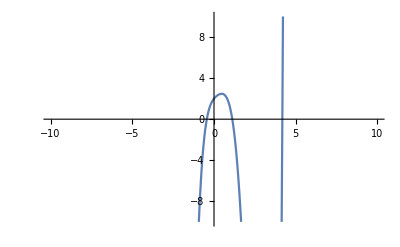

```mathematica
Plot[f[x],{x,-10,10},PlotRange->{{-10,10},{-10,10}}]
```

```mathematica
NSolve[f[x]==0,x]
```

{{x→-0.439386},{x→0.0696359-0.983851 ⅈ},{x→0.0696359+0.983851 ⅈ},{x→1.11912},{x→4.181}}

The first real solution...

```mathematica
Clear[g,h]
g[x_]:=5Cos[x]
h[x_]:=x
```

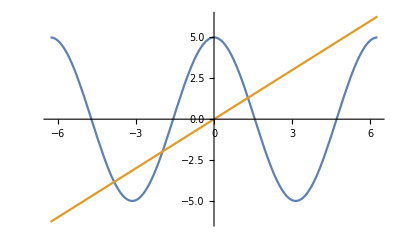

```mathematica
Plot[{g[x],h[x]},{x,-2π,2π}]
```

```mathematica
NSolve[g[x]-h[x]==0,x]
```

NSolve[-x+5 Cos[x]==0,x]

NSolve::nsmet: "This system cannot be solved with the methods available to NSolve."

```mathematica
Clear[myList]
myList={1.3,-2,-3.8}
```

{1.3,-2,-3.8}

```mathematica
FindRoot[g[x]==h[x],{x,1.3}]
```

{x→1.30644}

```mathematica
FindRoot[g[x]==h[x],{x,-2}]
```

{x→-1.97738}

```mathematica
FindRoot[g[x]==h[x],{x,-3.8}]
```

{x→-3.83747}

```mathematica
Trace[Table[FindRoot[g[x]==h[x],{x,i}],{i,myList}]]
```

{Table[FindRoot[g[x]==h[x],{x,i}],{i,myList}],{FindRoot[g[x]==h[x],{x,i}],{{i,1.3},{x,1.3}},{{i,1.3},{x,1.3}},{{g[x],5 Cos[x]},{h[x],x},5 Cos[x]==x},{{x}=.,{x=.},{x=.,Null},{Null}},{x→1.30644},{x→1.30644,x→1.30644},{x→1.30644}},{FindRoot[g[x]==h[x],{x,i}],{{i,-2},{x,-2}},{{i,-2},{x,-2}},{{g[x],5 Cos[x]},{h[x],x},5 Cos[x]==x},{{x}=.,{x=.},{x=.,Null},{Null}},{x→-1.97738},{x→-1.97738,x→-1.97738},{x→-1.97738}},{FindRoot[g[x]==h[x],{x,i}],{{i,-3.8},{x,-3.8}},{{i,-3.8},{x,-3.8}},{{g[x],5 Cos[x]},{h[x],x},5 Cos[x]==x},{{x}=.,{x=.},{x=.,Null},{Null}},{x→-3.83747},{x→-3.83747,x→-3.83747},{x→-3.83747}},{{x→1.30644},{x→-1.97738},{x→-3.83747}}}

```mathematica
Clear[t]
t[x_]:=(x-1)/(x^4-1)
```

```mathematica
Limit[t[x],x->1,Direction->-1]
```

1/4

```mathematica
Limit[t[x],x->1,Direction->1]
```

1/4

Because the limit of t(x) approaches 1/4 from the left and right...

```mathematica
Clear[p]
p[x_]:=Piecewise[{{x^2, x≤1}, {x+3, x>1}}]
```

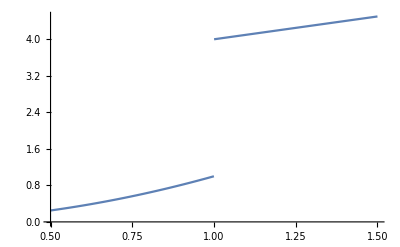

```mathematica
Plot[p[x],{x,.5,1.5}]
```

```mathematica
Limit[p[x],x->1,Direction->-1]
```

4

```mathematica
Limit[p[x],x->1,Direction->1]
```

1

```mathematica
Clear[t]
2 t^2+7t+3//Factor
```

(3+t) (1+2 t)

```mathematica
t^3-1//Factor
```

(-1+t) (1+t+t^2)

```mathematica
x^3+125//Factor
```

(5+x) (25-5 x+x^2)